# Analysis of Personal Fitness Data

Vlad DobrinAuthorInclude full name and credentials for all authors.Click for more information

AbstractAn abstract summarizes the most important points in your essay.
	◼ Summarize your most important content in about 100 words.
	◼ Provide a concise overview of the essay's conversation.
	◼ Highlight the motivations and scope.
	◼ Pay attention to the target audience.

Example:
Public-key cryptography, also known as asymmetric cryptography, uses two different but mathematically linked keys, one public and one private. In Rivest–Shamir–Adleman (RSA) cryptography, both the public and the private keys can encrypt a message; the opposite key from the one used to encrypt a message is used to decrypt it. Using RSA, we show how to encrypt messages between two users.
Click for more informationExploratory analysis of fitness data that was collected from the beginning of the year to 8/11

This projects looks at the data that can be collected from the Apple Watch. The analysis focuses on predictions that can be made from different types of workouts, visualizations of embedded data, and, of course, Machine Learning to classify and predict various aspects of future data.

## Questions:

The major question are as follows:

Is there an underlying structure that allows itself to be analyzed?

What is the best way to perform the analysis (list, association, dataset)?

What aspects of the data need to be processed and cleaned?

What interesting visualizations can be produced?

Can Machine Learning be applied? And if so, How?

## Start

Before running the initialization cells do the following: 
1) Open "All Data Cleaned and Put Into Correct Format...". Open "Interlude because of ...". And put in file path for route.csv
2) Open "Now there has been a lot of talk about Face Masks". And put file path for OTFWrkt.csv
3) Run initialization cell to do data cleaning and formatting.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
workoutData= Import["Workouts.csv"];
```

## Data Cleaning

### This Section deals with Hot Deck Imputation

```mathematica
(*Here I go about creating the hot deck imputation for any missing average heart rate or max heart rate for running data.*)
copyWMissingWD = workoutData;
```

```mathematica
smallerDataSetRunning = Cases[copyWMissingWD, {"Outdoor Running", ___}]; (*has all running data only*)
missing = Cases[copyWMissingWD, {"Outdoor Running", ___, "NA", ___}] ;(*has only running data with missing heart rate*) (*will generate output if there is missing data to match the pattern described*)
goodSamples = DeleteCases[smallerDataSetRunning, {"Outdoor Running", ___, "NA", ___}]; (*All the good samples for the running data*)
```

```mathematica
misLength = missing//Length;
```

```mathematica
For[HR = 6, HR< 8, HR++,
For[mis = 1, mis <= misLength, mis++,
Nearest[goodSamples[[All, {5,9,10,11}]], missing[[mis]][[{5,9,10,11}]]]; (*The value of missing[[mis]] the mis will be changed based on which entry we are trying to make a value for based on the list of missing produced*)
samples = # [[{5,9,10,11}]] -> #[[HR]] & /@ goodSamples; (*On this line the number 7 means max heart rate and number 6 means average heart rate, this can be used to calculate the correct values*)
replacement = Nearest[samples, missing[[mis]][[{5,9,10,11}]]]; (*This calculates the replacement value based on the nearest given from the sample the value inside missing[[mis]] mis has to be chosen to match the mis from the first line of code in this block*)
(*the values for 95,110,157 were extracted and put into individual if statements corresponding to the equivalent mis taken from the missing list*)
If[mis ==1,
copyWMissingWD[[95, HR]] = replacement;
copyWMissingWD[[95, HR]]= StringTake[ToString[copyWMissingWD[[95, HR]]], {2,4}]] ;(*The output of the replacement is put into either spot 6 (average heart rate) or 7 (max heart rate) and the first number in the pair copyWMissingWD[[x, HR]] x will be the row in which to change the value. This is where in the Workouts.csv it was exported as NA due to bad reading during run *)
(*This is used in order to take the hot deck imputation and then to create a new spreadsheet with all the filled in data.*)
If[mis ==2,
copyWMissingWD[[110, HR]] = replacement;
copyWMissingWD[[110, HR]] = StringTake[ToString[copyWMissingWD[[110, HR]]], {2,4}];];
If[mis ==3,
copyWMissingWD[[157, HR]] = replacement;
copyWMissingWD[[157, HR]]= StringTake[ToString[copyWMissingWD[[157, HR]]], {2,4}];]]]
```

### If Elevation was empty changed it to 0 if empty

Now to See if any elevation ascended does not have elevation when looking at running data

```mathematica
smallerDataSetRunning = Cases[copyWMissingWD, {"Outdoor Running", ___}];
```

```mathematica
missing = Cases[copyWMissingWD, {"Outdoor Running", ___, "", ___}];  (*Is used to check which elements have missing information based on specified pattern*)
```

```mathematica
lengthOut =copyWMissingWD //Length;
```

```mathematica
For[ i = 1, i < lengthOut, i++,
If[copyWMissingWD[[i,12]] == "",
copyWMissingWD[[i,12]]= 0  ] ]; (*Run loop to make all elevation 0 if is empty*)
```

### Distance needs to be sent to zero if empty

```mathematica
For[ i = 1, i < lengthOut, i++,
If[copyWMissingWD[[i,5]] == "",
copyWMissingWD[[i,5]]= 0  ] ]; (*Run loop to make all distance 0 if is empty*)
```

### Average Pace and Average Speed sent to zero if empty

```mathematica
For[ i = 1, i < lengthOut, i++,
If[copyWMissingWD[[i,8]] == "",
copyWMissingWD[[i,8]]= 0  ] 
If[copyWMissingWD[[i,9]] == "",
copyWMissingWD[[i,9]]= 0  ]
]; (*Run loop to make all pace/speed 0 if is empty*)
```

### Convert cleaned data to excel file

```mathematica
copyWMissingWD //TableForm;
Export["CleanedDataWorkouts2.csv", copyWMissingWD]
```

CleanedDataWorkouts2.csv

## Import Clean Data

The reason for the need to import the second spreadsheet was because after all data cleaning was done, a second collection source (emailed data from OTBeat, which collected treadmill data) was used to manually input average pace and average speed for specific High Intensity Interval Training data. This was done because there was no way (to my knowledge from bootcamp) to get data from email into Mathematica.

```mathematica
workoutData = Import["CleanedDataWorkouts.csv"];
```

## Change Start to DateObject

```mathematica
copyWorkoutData = workoutData ;
```

```mathematica
lengthRow = workoutData // Length;
```

```mathematica
(*This gives a ambiguous warning which is not needed*)
For[j = 2, j < lengthRow, j++,copyWorkoutData[[j,2]] = DateObject[DateString[workoutData[[j,2]]]]  ]
```

DateObject::ambig: Warning: the interpretation of the string 7/11/2020 17:50 as a date is ambiguous.

DateObject::ambig: Warning: the interpretation of the string 7/9/2020 18:32 as a date is ambiguous.

DateObject::ambig: Warning: the interpretation of the string 7/9/2020 18:17 as a date is ambiguous.

General::stop: Further output of DateObject::ambig will be suppressed during this calculation.

## Change End to DateObject

```mathematica
lengthRow = workoutData // Length;
```

```mathematica
(*This gives a ambiguous warning which is not needed*)
For[j = 2, j < lengthRow, j++,copyWorkoutData[[j,3]] = DateObject[DateString[workoutData[[j,3]]]]  ]
```

DateObject::ambig: Warning: the interpretation of the string 7/11/2020 18:38 as a date is ambiguous.

DateObject::ambig: Warning: the interpretation of the string 7/9/2020 18:38 as a date is ambiguous.

DateObject::ambig: Warning: the interpretation of the string 7/9/2020 18:23 as a date is ambiguous.

General::stop: Further output of DateObject::ambig will be suppressed during this calculation.

## Change Duration to TimeObject

```mathematica
lengthRow = workoutData // Length;
```

```mathematica
For[j = 2, j < lengthRow, j++,copyWorkoutData[[j,4]] = TimeObject[DateString[workoutData[[j,4]]]]  ]
```

## Change Distance, HR, Speed, Calories, Elevation, Temp, Humidity String -> Real

Change the Type from String to Real for Distance

```mathematica
lengthOut = workoutData  // Length;
lengthRow = workoutData[[1]] // Length;
```

5 = distance, 6 = AVG HR, 7 = Max HR, 9 = Avg Speed, 10 = Active Energy, 11 = Total Energy, 12 = Elevation Ascended, 13 = Temp, 14 = Humidity

Loop to turn the above into Reals the way they should be, string are not helpful to me...

```mathematica
For[j = 5, j < lengthRow; j++,
a = ToExpression /@ Rest[workoutData[[All, j]]];
For[i = 2, i < lengthOut, i++,
If[j ≠ 8,
copyWorkoutData[[i,j]] = a[[i - 1]]]]]
```

## Change Average Pace to TimeObject

```mathematica
lengthRow = workoutData // Length;
```

```mathematica
For[j = 2, j < lengthRow, j++,copyWorkoutData[[j,8]] = TimeObject[DateString[workoutData[[j,8]]]]  ]
```

## All Data Cleaned and Put Into Correct Format: Moving to Exploration/Analysis

### Max HR vs Calories Burned Interesting Conclusions

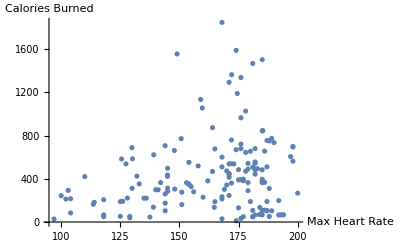

```mathematica
toolTip = Tooltip[#[[{7,10}]],Grid[{{"Workout Type",#[[1]]}, {"Max Heart Rate",#[[7]]}, {"Distance",#[[5]]} },Frame->All]]&/@ workoutData;
ListPlot[toolTip, AxesLabel-> {"Max Heart Rate", "Calories Burned"}]
```

OUTLIERS:
Left top outlier (149, 1556.98) was a 60 mile bike ride to Washington DC
Top Right outlier (168, 1848.79) was 2:30 hour trail run through the Appalachian trail in Virginia

### Interlude because of that top left outlier

```mathematica
(*Location of route.csv must be given*)
bike = Import["C:\\Users\\vlada\\OneDrive\\Documents\\Wolfram Data Science Boot Camp\\DcBike\\route.csv"];
```

We see the change in altitude vs the latitude and longitude. 
Destination is below the starting place, not making for a fun ride back.
For those of you curious about the dip in the middle: There is a BIG hill in Bethesda in front of the NIH.

```mathematica
latLong=bike[[2;;,{2,3}]];
latLongAlt=bike[[2;;,{2,3,4}]];

altplot=ListPointPlot3D[latLongAlt,Filling->None,BoxRatios->{Automatic,Automatic,.04},ColorFunction->(ColorData["Rainbow",2.5 (#3-0.6)]&),AxesLabel->{"latitude","longitude","altitude"},ImageSize->Large];

Show[altplot]
```

-Graphics3D-

Manipulable map of the bike ride itself. (Can be performed on any route given the csv file)

```mathematica
Manipulate[GeoGraphics[GeoPath[Take[bike[[2;;,{2,3}]],UpTo[pointsToShow]]],GeoRange->{{38.88955563,39.17498885},{-77.11620704,-77.03317762}}, GeoBackground->Automatic],{{pointsToShow,0,"Cycling distance"},0,Length[latLong],AnimationRate->bike[[All,8]][[pointsToShow]],AnimationDirection->Forward},SaveDefinitions->True]
```

### Return to Where We Left Off

This is looking at the type of workouts and where they fall.

Red is low level recovery training.
Brown is Soccer practice/ Strength Training - Lots of time standing/ Resting

These are all stacked, not much of a surprise when you think about it...
Blue is sprint workouts 20- 30 minute
Yellow is mid distance workouts 30 - 40 minute
Green is Long workouts 40 minutes - 1:30 hour
Purple is the aerobic base training 1:30 Hour plus

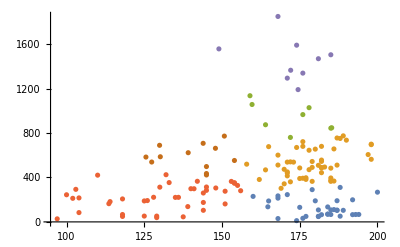

```mathematica
workoutDataNoHeader = workoutData[[2;;]];
aData = Association[#[[{1,2,4}]] -> #[[{7,10}]] & /@ workoutDataNoHeader];
cls = FindClusters[aData];
ListPlot[Map[ Tooltip@@@Transpose[{aData /@ #, #}]&, cls]]
```

### Unexpected Result of Heart Rate vs Elevation

It would have been expected to see a linear increase between AVG Heart Rate and elevation, but this does not seem to be the case! 
Potential Reasons: Pacing

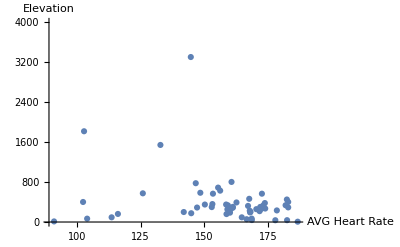

```mathematica
len = workoutData //Length;
workoutDataWO0Elev = workoutData;
For[i = 2, i < len,i++, 
If[workoutData[[i,12]] === 0, workoutDataWO0Elev[[i,12]] = Missing]] 

ListPlot[workoutDataWO0Elev[[2;;, {6,12}]], AxesLabel-> {"AVG Heart Rate", "Elevation"}, PlotRange->{0,4000}]
```

If however the outliers are removed (anything with change in elevation of greater than 1200 ft) The trend is supported!

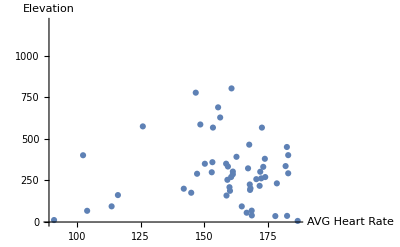

```mathematica
len = workoutData //Length;
workoutDataWO0Elev = workoutData;
For[i = 2, i < len,i++, 
If[workoutData[[i,12]] === 0, workoutDataWO0Elev[[i,12]] = Missing]] 
For[i = 2, i < len,i++, 
If[workoutData[[i,12]] > 1200, workoutDataWO0Elev[[i,12]] = Missing]] 

ListPlot[workoutDataWO0Elev[[2;;, {6,12}]], AxesLabel-> {"AVG Heart Rate", "Elevation"}, PlotRange->{0,1200}]
```

### Heart Rate Machine Learning

#### MACHINE LEARNING!

```mathematica
workoutDataDataSet= copyWorkoutData; (*Making copy*)
len =workoutDataDataSet //Length; (*Length for loop*)
finalAssociation = {}; (*place of storage for the association*)

For[i = 2,i <len, i++,
curr= AssociationThread[{"Type", "Start", "End", "Duration", "Distance", "Average Heart Rate", "Max Heart Rate", "Average Pace", "Average Speed", "Active Energy", "Total Energy", "Elevation Ascended", "Weather Temperature", "Weather Humidity"},workoutDataDataSet[[i,;;]]];
finalAssociation =Append[finalAssociation, curr]  ](*turns everything from list of list to association*)

workoutDataDataSet = finalAssociation //Dataset;(*Used to set back to correct spot and make it a dataset*)
```

```mathematica
workoutDataDataSet = RandomSample[workoutDataDataSet];
trainingSet = workoutDataDataSet[[;;78]];
testSet = workoutDataDataSet[[79;;]];
p = Predict[trainingSet -> "Average Heart Rate"]
```

PredictorFunction[…]

```mathematica
Information[p, "LearningCurve"]
```

```mathematica
pm = PredictorMeasurements[p, testSet -> "Average Heart Rate"]
```

PredictorMeasurementsObject[…]

```mathematica
pm["StandardDeviation", ComputeUncertainty -> True]
```

18.01.3

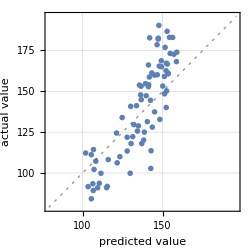
Predictor Measurements
Number of test examples | 78
Standard deviation | 18. ± 1.3
Standard deviation baseline | 29.2 ± 1.5
Mean cross entropy | 4.67 ± 0.015
Single evaluation time | 19.8 ms/example
Batch evaluation speed | 163. examples/s
-Graphics- |

```mathematica
pm["Report"]
```

By simple examination the best predicted example is clean data, the worst predicted probably had a bad reading on me on the day of. The worst predicted example was for a 1000M sprint. This can be expected because the average heart rate would be very high for a sprint and sufficient data was not provided to train on varying training types.

```mathematica
pm["BestPredictedExamples"->1]
```

{{Traditional Strength Training,Minute: Wed 20 May 2020 15:51GMT-4.,Minute: Wed 20 May 2020 16:21GMT-4.,00:30:01TimeObject[{0,30,1.},Instant,None],0,139,00:00:00TimeObject[{0,0,0.},Instant,None],0,137.755,186.385,0,61,49}→107.189}

```mathematica
pm["WorstPredictedExamples"->1]
```

{{Outdoor Running,Minute: Thu 7 May 2020 13:20GMT-4.,Minute: Thu 7 May 2020 13:23GMT-4.,00:03:27TimeObject[{0,3,27.},Instant,None],0.604593,193,00:05:43TimeObject[{0,5,43.},Instant,None],10.4774,66.567,72.629,0,60,31}→190.333}

### Unsupervised predict type of workout

```mathematica
workoutDataDataSet= copyWorkoutData; (*Making copy*)
len =workoutDataDataSet //Length; (*Length for loop*)
finalAssociation = {}; (*place of storage for the association*)

For[i = 2,i <len, i++,
curr= AssociationThread[{"Type", "Start", "End", "Duration", "Distance", "Average Heart Rate", "Max Heart Rate", "Average Pace", "Average Speed", "Active Energy", "Total Energy", "Elevation Ascended", "Weather Temperature", "Weather Humidity"},workoutDataDataSet[[i,;;]]];
finalAssociation =Append[finalAssociation, curr]  ](*turns everything from list of list to association*)

workoutDataDataSet = finalAssociation //Dataset;(*Used to set back to correct spot and make it a dataset*)
```

```mathematica
listForUnsML = {}
```

{}

```mathematica
(*This turns the dataset into a association that can be used for ML*)
For[i = 2, i < 158, i++, 
listForUnsML = Append[listForUnsML, copyWorkoutData[[i,2;;]] -> copyWorkoutData[[i,1]]]
]
```

```mathematica
listForUnsML = RandomSample[listForUnsML];
```

```mathematica
trainingsetUn = listForUnsML[[;; 78]];
testsetUn = listForUnsML[[79;;]];
```

```mathematica
cUn = Classify[trainingsetUn]
```

ClassifierFunction[…]

```mathematica
Information[cUn]
```

Classifier information
Data type | Mixed (number: 13)
Number of classes | 9
Accuracy | (77.8.) %
Method | LogisticRegression
Single evaluation time | 27.1 ms/example
Batch evaluation speed | 162. examples/s
Loss | 0.866 ± 0.17
Model memory | 367. kB
Training examples used | 78 examples
Training time | 3.75 s
 |

```mathematica
cmUn = ClassifierMeasurements[cUn, testsetUn]
```

ClassifierMeasurementsObject[…]

```mathematica
cmUn["Accuracy", ComputeUncertainty -> True]
```

0.860.04

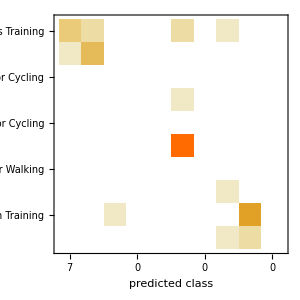

```mathematica
cmUn ["ConfusionMatrixPlot"]
```

### Indoor walking/ Running seems to have caused lots of problems let us remove and try again.

```mathematica
listforTryTwo = {}
```

{}

```mathematica
For[i = 2, i < 158, i++, 
If[copyWorkoutData[[i,1]]≠ "Indoor Walking" && copyWorkoutData[[i,1]]≠ "Indoor Running" ,
listforTryTwo = Append[listforTryTwo, copyWorkoutData[[i,2;;]] -> copyWorkoutData[[i,1]]]
]]
```

```mathematica
listforTryTwo  //Length;
```

```mathematica
listforTryTwo = RandomSample[listforTryTwo];
```

```mathematica
trainingsetUn = listforTryTwo[[;; 74]];
testsetUn = listforTryTwo[[75;;]];
```

```mathematica
cUn = Classify[trainingsetUn]
```

ClassifierFunction[…]

```mathematica
Information[cUn]
```

Classifier information
Data type | Mixed (number: 13)
Number of classes | 7
Accuracy | (76.16.) %
Method | RandomForest
Single evaluation time | 23.6 ms/example
Batch evaluation speed | 178. examples/s
Loss | 1.38 ± 0.14
Model memory | 435. kB
Training examples used | 74 examples
Training time | 2.64 s
 |

```mathematica
cmUn = ClassifierMeasurements[cUn, testsetUn]
```

ClassifierMeasurementsObject[…]

```mathematica
cmUn["Accuracy", ComputeUncertainty -> True]
```

0.880.04

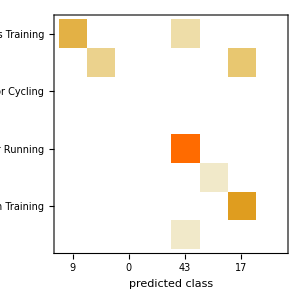

```mathematica
cmUn ["ConfusionMatrixPlot"]
```

Able to predict the type of workout about 9/10 of the time after removing indoor walking/ running. Further more the error or cross training, outdoor running and HIIT is also predictable because of the high intensity nature and distance covered. This could be avoided by increasing the distance on outdoor runs vs cross training sessions vs HIIT Sessions.

### Fun Facts and Statistics

We can see the predominant workout types in this manner for the time period 1/1/2020 -> 7/24/2020

```mathematica
hist = Tally[workoutDataDataSet[[All,"Type"]]];
label = hist[[All, 1]] // Normal;
BarChart[hist[[All, 2]], ChartStyle->"Pastel", ChartLabels->Callout[label]]
```

-Graphics-

Number of days being analyzed:

```mathematica
DateDifference[DateObject[{2020,1,1},"Day","Gregorian",-6.],DateObject[{2020,7,24},"Day","Gregorian",-6.]]
```

205 days

Number of workouts performed in that time period:

```mathematica
workoutDataDataSet //Length
```

156

Works out to

```mathematica
N[156/205]
```

0.760976

workouts per day. Which means 5 days of the week are spent workout out 2 resting!

It can even be visualized on a timeline when the workouts occurred.

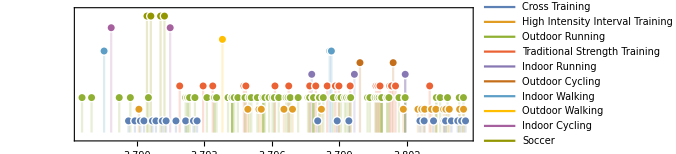

```mathematica
dates = Normal[GroupBy[workoutDataDataSet, "Type"][All,All,"Start"]];
TimelinePlot[Values[dates], Filling->Axis, PlotLegends->Keys[dates]]
```

## Now there has been a lot of talk about Face Masks

With the reopening of gyms some gyms require face mask while working out and others do not.  I have had the opportunity to train at 2 gyms. One requires face masks the other does not, let us see if anything interesting has come out of this.

```mathematica
(*This data is already cleaned apple watch here gave me everything I needed. All I need to do is put into correct formats like done above.*)
```

```mathematica
(*Ensure Import Location is correct*)
OTF= Import["C:\\Users\\vlada\\OneDrive\\Documents\\Wolfram Data Science Boot Camp\\OTFwrkt.csv"];
```

### Change Start to DateObject

```mathematica
copyOTF = OTF ;
```

```mathematica
lengthRowOTF = OTF // Length;
```

```mathematica
(*This gives a ambiguous warning which is not needed*)
For[j = 2, j < lengthRowOTF, j++,copyOTF[[j,2]] = DateObject[DateString[StringDrop[OTF[[j,2]], -5]]] ]
```

DateObject::ambig: Warning: the interpretation of the string 8/11/2020 as a date is ambiguous.

DateObject::ambig: Warning: the interpretation of the string 8/10/2020  as a date is ambiguous.

DateObject::ambig: Warning: the interpretation of the string 8/4/2020  as a date is ambiguous.

General::stop: Further output of DateObject::ambig will be suppressed during this calculation.

### Change End to DateObject

```mathematica
(*This gives a ambiguous warning which is not needed*)
For[j = 2, j < lengthRowOTF, j++,copyOTF[[j,3]] = DateObject[DateString[copyOTF[[j,3]]]] ]
```

DateObject::ambig: Warning: the interpretation of the string 8/11/2020 10:26 as a date is ambiguous.

DateObject::ambig: Warning: the interpretation of the string 8/10/2020 13:29 as a date is ambiguous.

DateObject::ambig: Warning: the interpretation of the string 8/4/2020 17:33 as a date is ambiguous.

General::stop: Further output of DateObject::ambig will be suppressed during this calculation.

### Change Duration to TimeObject

```mathematica
For[j = 2, j < lengthRowOTF, j++,copyOTF[[j,4]] = TimeObject[DateString[copyOTF[[j,4]]]] ]
```

### Change Distance, HR, Speed, Calories, Elevation, Temp, Humidity String -> Real

Change the Type from String to Real for Distance

```mathematica
lengthRowOTF = OTF // Length;
lengthOutOTF = OTF[[1]] // Length;
```

5 = distance, 6 = AVG HR, 7 = Max HR, 9 = Avg Speed, 10 = Active Energy, 11 = Total Energy, 12 = Elevation Ascended, 13 = Temp, 14 = Humidity

Loop to turn the above into Reals the way they should be, string are not helpful to me...

```mathematica
(*OTF*)
For[j = 5, j < lengthOutOTF; j++,
a = ToExpression /@ Rest[OTF[[All, j]]];
For[i = 2, i < lengthRowOTF, i++,
If[j ≠ 8,
copyOTF[[i,j]] = a[[i - 1]]]]]
```

### Change Average Pace to TimeObject

```mathematica
For[j = 2, j < lengthRowOTF, j++,copyOTF[[j,8]] = TimeObject[DateString[copyOTF[[j,8]]]] ]
```

### Preface

The types of workouts explored here are High Intensity Interval Training and the time to return to pre pandemic levels of fitness as based off of distance covered throughout the workout and speed achieved.

### Visuals:

```mathematica
copyOTFDataSet= copyOTF; (*Making copy*)
len =copyOTFDataSet //Length; (*Length for loop*)
OTFAssociation = {}; (*place of storage for the association*)

For[i = 2,i <len, i++,
curr= AssociationThread[{"Type", "Start", "End", "Duration", "Distance", "Average Heart Rate", "Max Heart Rate", "Average Pace", "Average Speed", "Active Energy", "Total Energy", "Elevation Ascended", "Weather Temperature", "Weather Humidity"},copyOTFDataSet[[i,;;]]];
OTFAssociation =Append[OTFAssociation, curr]  ](*turns everything from list of list to association*)

OTFDataSet = OTFAssociation //Dataset;(*Used to set back to correct spot and make it a dataset*)
```

```mathematica
(*Need to put distances run over time and see model for best fit*)
dist = OTFDataSet[All, "Distance"] //Normal;
```

```mathematica
fitted =LinearModelFit[Reverse[dist],x,x];
fittedLog = NonlinearModelFit[Reverse[dist],Log[a*x],{a},x];
```

```mathematica
(*A logarithmic model fits the pace of improvment much better*)
```

```mathematica
fitted["RSquared"]
```

0.737555

```mathematica
fittedLog["RSquared"]
```

0.970846

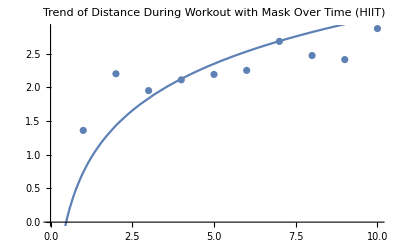

```mathematica
Show[ListPlot[Reverse[dist]], Plot[{fittedTwo[x]}, {x,-5, 15}, AspectRatio->Full],  PlotLabel->"Trend of Distance During Workout with Mask Over Time (HIIT)"]
```

```mathematica
(*Distance is great but now need to see how many classes were needed to get back to pre covid speed*)
```

```mathematica
speed = OTFDataSet[All, "Average Speed"] //Normal;
fittedS =LinearModelFit[Reverse[speed],x,x];
fittedLogS = NonlinearModelFit[Reverse[speed],Log[a*x],{a},x];
fittedS["RSquared"]
fittedLogS["RSquared"]
(*Logarithmic is even more accurate for speed*)
```

0.146354

0.990788

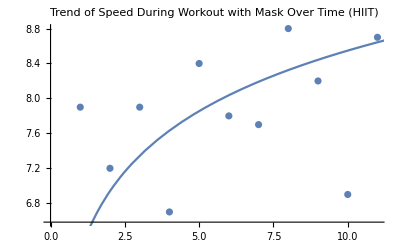

```mathematica
Show[ListPlot[Reverse[dist]], Plot[{fittedTwoS[x]}, {x,-5, 15}, AspectRatio->Full],  PlotLabel->"Trend of Speed During Workout with Mask Over Time (HIIT)"]
```

Conclusion: Based on coach recommendation of 1 mph pull back the adjustment from 6.5 to 7.5 pace would only take about 4-6 classes! Mask training only takes about 4-6 classes to adjust. Much faster than expected!

## Future Direction

The ultimate goal with this project is to generate level of exertion to predict rest days and muscle recovery needs. It will be necessary to implement other data such as sleep data and yoga data. Both of the aforementioned pieces of data would serve as recovery parameters.

## KeywordsKeywordsInfoButtonList relevant terms that should be used to include the essay in search results.Click for more information

Heart Rate

Machine Learning

Supervised Machine Learning

Unsupervised Machine Learning

Elevation

Data Science

Unsupervised: Predict type of workout based on input parameters.